```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Практика\\Программа\\project"]
```

C:\Users\griho\OneDrive\Рабочий стол\Практика\Программа\project

```mathematica
(* Алгоритм Киркпатрика *)
flipped[points_List]:=Map[{-#[[1]], -#[[2]]}&,points]

bridge[points_List, med_, eps_:10.^-12] := Block[{candidates = If[EvenQ@Length@points,{},{Last@points}], pairs={},
k ={}, kMed,maxSlope,
small={}, equal={}, large={},
max, pK, pM},
(* шаги 2 и 3 *)
If[Length@points == 2, Return@SortBy[{points[[1]],points[[2]]},First]];
For[i=1,i<Length@points,i=i+2,If[Abs[points[[i,1]]-points[[i+1,1]]]<eps,
AppendTo[candidates,If[points[[i,2]]>points[[i+1,2]], points[[i]],points[[i+1]]]], 
AppendTo[k, (points[[i,2]]-points[[i+1,2]])/(points[[i,1]]-points[[i+1,1]])];AppendTo[pairs,SortBy[{points[[i]],points[[i+1]]},First]]
]];
(* шаг 4 *)
kMed = Median[k];
(* шаг 5 *)
For[i = 1, i<= Length@pairs, i++, Which[Abs[k[[i]]-kMed]<eps,AppendTo[equal,pairs[[i]]],
k[[i]] < kMed,AppendTo[small,pairs[[i]]],
True,AppendTo[large,pairs[[i]]]]];
(* шаг 6 *)
maxSlope=Max@Map[#[[2]] - kMed #[[1]]&, points];
max = Select[points, Abs[#[[2]] - kMed #[[1]]-maxSlope]<eps&];
(* pK и pM могут быть равны *)
pK = MinimalBy[max, #[[1]]&][[1]];
pM = MaximalBy[max, #[[1]]&][[1]];
(* шаг 7 *)
(*TODO сравнение вещественных чисел*)
If[(Abs[pK[[1]]-med]<eps || pK[[1]]<med) && pM[[1]] > med, Return[{pK, pM}],
(* шаг 8 *)
(*TODO сравнение вещественных чисел*)
(*иначе если*)
If[ Abs[pM[[1]]-med ]<eps|| pM[[1]]< med,candidates = candidates~Join~Map[#[[2]]&, large~Join~equal];candidates =candidates~Join~Flatten[small,1],
(* шаг 9 *)
(*иначе*)candidates = candidates~Join~Map[#[[1]]&, small~Join~equal];candidates =candidates~Join~Flatten[large,1]]];
bridge[candidates, med]
]

connect[min_, max_, points_List] := Block[{a=Median@Map[#[[1]]&,points],b,left, right, SLeft,SRight},
b=bridge[points, a];
left = b[[1]]; right = b[[2]];
(*TODO сравнение вещественных чисел, но это вроде норм*)
SLeft = If[min==left,{min},connect[min,left,Select[points,#[[1]] < left[[1]]&]~Join~{left}]];
SRight = If[max==right,{max},connect[right,max,{right}~Join~Select[points,#[[1]] > right[[1]]&]]];
SLeft~Join~SRight
]

upperHull[points_List] := Block[{
min = MaximalBy[MinimalBy[points,#[[1]]&], #[[2]]&][[1]],
max=MaximalBy[MaximalBy[points,#[[1]]&], #[[2]]&][[1]],
minY},
minY=Min[max[[2]],min[[2]]];
connect[min,max, Select[points, #[[2]]>=minY&]]
]
(*чтобы не писать один алгоритм дважды,мы просто отражаем картинку и снова рассматриваем верхнюю границу*)
lowerHull[points_List] := flipped@upperHull@flipped@points

KirkpatrickSeidelConvexHull[points_List]:= Block[{upper = upperHull@points, lower = lowerHull@points},
If[Last@upper == First@lower, upper = Most@upper];
If[First@upper == Last@lower, upper = Rest@upper];
upper~Join~lower
]
KSAlgFromFile[from_, to_]:= Block[{data=Rest@Import[from, "Table"], res, time},{time,res}=KirkpatrickSeidelConvexHull[data]//Timing;Export[to,{Length@res}~Join~res, "Table"]; Print[res];time ]
```

```mathematica
(*вспомогательные функции для изучения и визуализации результата алгоритма*)
visualization[src_List, res_List, joined_:True] := ListPlot[{src, Append[res, res[[1]]]}, Joined->{False, joined}, AspectRatio->Automatic]
ksTesting[data_] := Block[{time, res}, {time,res}=KirkpatrickSeidelConvexHull@data//Timing;Print[time, "; ", Length@res];Print[visualization[data, res]]; res]
generateTest[count_:50] := Block[{data = RandomReal[{-1, 1}, {count, 2}], time, res}, {time,res}=KirkpatrickSeidelConvexHull@data//Timing;Print[data];Print[time];visualization[data, res]]
```

{{0.467764,-0.0999723},{0.339727,-0.321517},{-0.284286,0.262691},{0.885774,-0.875109},{-0.68703,0.607017},{0.452984,-0.64844},{-0.835368,0.342253},{0.013645,0.251921},{0.425701,0.641089},{0.615464,0.473149},{-0.00941125,0.885202},{-0.0000387159,-0.395146},{0.0942639,-0.321131},{0.355413,-0.0261107},{0.685859,-0.476604},{-0.324744,0.0112429},{0.851285,0.668656},{0.507474,-0.0331661},{-0.373681,0.838841},{0.055195,-0.101178},{-0.599996,-0.696574},{0.93717,0.0212218},{-0.897074,-0.736431},{0.255865,0.246444},{0.316297,0.141609},{0.203011,0.958093},{0.445646,-0.647884},{0.888933,0.642512},{0.666248,0.743372},{0.631156,0.874197},{-0.43556,-0.29297},{-0.0615173,-0.686418},{-0.289891,0.25995},{0.397044,-0.22511},{0.0080411,-0.63599},{-0.547958,-0.534},{0.750974,0.592041},{-0.264314,0.838766},{-0.54211,0.564446},{0.569674,0.0140564},{0.571149,0.0606623},{-0.218321,-0.824471},{0.562759,0.587793},{-0.179813,-0.387964},{-0.93145,0.029097},{0.491795,0.858923},{0.0449531,0.761077},{0.9084,0.212296},{0.218619,-0.0398413},{-0.828201,-0.779267}}

0.015625

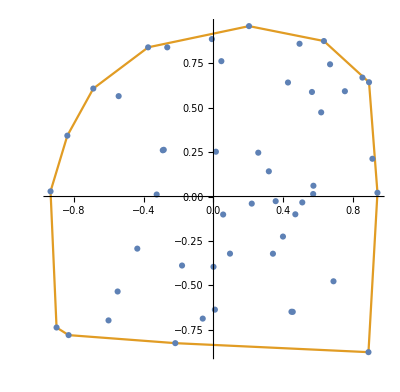

```mathematica
(*этот пример используется в презентации, раскрой меня*)
generateTest[]
```

```mathematica
spisok = Rest@Import["question.txt","Table"];
```

```mathematica
Length[result]
```

0

```mathematica
Timing@KirkpatrickSeidelConvexHull[spisok]
```

{0.28125,{{-0.999512,0.947508},{-0.998535,0.979797},{-0.763909,0.993408},{-0.355022,0.997253},{0.20658,0.999573},{0.784906,0.999207},{0.878475,0.995849},{0.947569,0.978027},{0.993225,0.841365},{0.999695,0.506882},{0.999878,0.19071},{0.999084,-0.268654},{0.986633,-0.882076},{0.982299,-0.975646},{0.821223,-0.995849},{0.229041,-0.998474},{-0.370647,-1},{-0.649098,-0.998169},{-0.909421,-0.988769},{-0.961974,-0.983581},{-0.97644,-0.925352},{-0.988525,-0.851375},{-0.996277,-0.588916},{-0.999878,-0.0851772}}}

```mathematica
Length[KirkpatrickSeidelConvexHull[spisok]]
```

24